# RandomBezierCurve

One-line description explaining the function’s basic purpose

## Definition

```mathematica
ClearAll[RandomBezierCurve]

RandomBezierCurve[count_?IntegerQ,{lower_,upper_},options:OptionsPattern[Graphics]]:=Graphics[BezierCurve[RandomReal[{lower,upper},{count,2}]],options]/;count>0

RandomBezierCurve[count_?IntegerQ,{lower_,upper_},2,options:OptionsPattern[Graphics]]:=Graphics[BezierCurve[RandomReal[{lower,upper},{count,2}]],options]/;count>0

RandomBezierCurve[count_?IntegerQ,{lower_,upper_},3,options:OptionsPattern[Graphics3D]]:=Graphics3D[BezierCurve[RandomReal[{lower,upper},{count,3}]],options]/;count>0



RandomBezierCurve[count_?IntegerQ,{lower_,upper_},"Real",options:OptionsPattern[Graphics]]:=Graphics[BezierCurve[RandomReal[{lower,upper},{count,2}]],options]/;count>0

RandomBezierCurve[count_?IntegerQ,{lower_,upper_},2,"Real",options:OptionsPattern[Graphics]]:=Graphics[BezierCurve[RandomReal[{lower,upper},{count,2}]],options]/;count>0

RandomBezierCurve[count_?IntegerQ,{lower_,upper_},3,"Real",options:OptionsPattern[Graphics3D]]:=Graphics3D[BezierCurve[RandomReal[{lower,upper},{count,3}]],options]/;count>0


RandomBezierCurve[count_?IntegerQ,{lower_,upper_},"Integer",options:OptionsPattern[Graphics]]:=Graphics[BezierCurve[RandomInteger[{lower,upper},{count,2}]],options]/;count>0

RandomBezierCurve[count_?IntegerQ,{lower_,upper_},2,"Integer",options:OptionsPattern[Graphics]]:=Graphics[BezierCurve[RandomInteger[{lower,upper},{count,2}]],options]/;count>0

RandomBezierCurve[count_?IntegerQ,{lower_,upper_},3,"Integer",options:OptionsPattern[Graphics3D]]:=Graphics3D[BezierCurve[RandomInteger[{lower,upper},{count,3}]],options]/;count>0

RandomBezierCurve[count_?IntegerQ,max_,options:OptionsPattern[Graphics]]:=Graphics[BezierCurve[RandomReal[max,{count,2}]],options]/;count>0

RandomBezierCurve[count_?IntegerQ,max_,2,options:OptionsPattern[Graphics]]:=Graphics[BezierCurve[RandomReal[max,{count,2}]],options]/;count>0

RandomBezierCurve[count_?IntegerQ,max_,3,options:OptionsPattern[Graphics3D]]:=Graphics3D[BezierCurve[RandomReal[max,{count,3}]],options]/;count>0



RandomBezierCurve[count_?IntegerQ,max_,"Real",options:OptionsPattern[Graphics]]:=Graphics[BezierCurve[RandomReal[max,{count,2}]],options]/;count>0

RandomBezierCurve[count_?IntegerQ,max_,2,"Real",options:OptionsPattern[Graphics]]:=Graphics[BezierCurve[RandomReal[max,{count,2}]],options]/;count>0

RandomBezierCurve[count_?IntegerQ,max_,3,"Real",options:OptionsPattern[Graphics3D]]:=Graphics3D[BezierCurve[RandomReal[max,{count,3}]],options]/;count>0


RandomBezierCurve[count_?IntegerQ,max_,"Integer",options:OptionsPattern[Graphics]]:=Graphics[BezierCurve[RandomInteger[max,{count,2}]],options]/;count>0

RandomBezierCurve[count_?IntegerQ,max_,2,"Integer",options:OptionsPattern[Graphics]]:=Graphics[BezierCurve[RandomInteger[max,{count,2}]],options]/;count>0

RandomBezierCurve[count_?IntegerQ,max_,3,"Integer",options:OptionsPattern[Graphics3D]]:=Graphics3D[BezierCurve[RandomInteger[max,{count,3}]],options]/;count>0


(*Style specifications*)
RandomBezierCurve[count_?IntegerQ,{lower_,upper_},style_,options:OptionsPattern[Graphics]]:=Graphics[{style,BezierCurve[RandomReal[{lower,upper},{count,2}]]},options]/;count>0

RandomBezierCurve[count_?IntegerQ,{lower_,upper_},2,style_,options:OptionsPattern[Graphics]]:=Graphics[{style,BezierCurve[RandomReal[{lower,upper},{count,2}]]},options]/;count>0

RandomBezierCurve[count_?IntegerQ,{lower_,upper_},3,style_,options:OptionsPattern[Graphics3D]]:=Graphics3D[{style,BezierCurve[RandomReal[{lower,upper},{count,3}]]},options]/;count>0



RandomBezierCurve[count_?IntegerQ,{lower_,upper_},"Real",style_,options:OptionsPattern[Graphics]]:=Graphics[{style,BezierCurve[RandomReal[{lower,upper},{count,2}]]},options]/;count>0

RandomBezierCurve[count_?IntegerQ,{lower_,upper_},2,"Real",style_,options:OptionsPattern[Graphics]]:=Graphics[{style,BezierCurve[RandomReal[{lower,upper},{count,2}]]},options]/;count>0

RandomBezierCurve[count_?IntegerQ,{lower_,upper_},3,"Real",style_,options:OptionsPattern[Graphics3D]]:=Graphics3D[{style,BezierCurve[RandomReal[{lower,upper},{count,3}]]},options]/;count>0


RandomBezierCurve[count_?IntegerQ,{lower_,upper_},"Integer",style_,options:OptionsPattern[Graphics]]:=Graphics[{style,BezierCurve[RandomInteger[{lower,upper},{count,2}]]},options]/;count>0

RandomBezierCurve[count_?IntegerQ,{lower_,upper_},2,"Integer",style_,options:OptionsPattern[Graphics]]:=Graphics[{style,BezierCurve[RandomInteger[{lower,upper},{count,2}]]},options]/;count>0

RandomBezierCurve[count_?IntegerQ,{lower_,upper_},3,"Integer",style_,options:OptionsPattern[Graphics3D]]:=Graphics3D[{style,BezierCurve[RandomInteger[{lower,upper},{count,3}]]},options]/;count>0

RandomBezierCurve[count_?IntegerQ,max_,style_,options:OptionsPattern[Graphics]]:=Graphics[{style,BezierCurve[RandomReal[max,{count,2}]]},options]/;count>0

RandomBezierCurve[count_?IntegerQ,max_,2,style_,options:OptionsPattern[Graphics]]:=Graphics[{style,BezierCurve[RandomReal[max,{count,2}]]},options]/;count>0

RandomBezierCurve[count_?IntegerQ,max_,3,style_,options:OptionsPattern[Graphics3D]]:=Graphics3D[{style,BezierCurve[RandomReal[max,{count,3}]]},options]/;count>0



RandomBezierCurve[count_?IntegerQ,max_,"Real",style_,options:OptionsPattern[Graphics]]:=Graphics[{style,BezierCurve[RandomReal[max,{count,2}]]},options]/;count>0

RandomBezierCurve[count_?IntegerQ,max_,2,"Real",style_,options:OptionsPattern[Graphics]]:=Graphics[{style,BezierCurve[RandomReal[max,{count,2}]]},options]/;count>0

RandomBezierCurve[count_?IntegerQ,max_,3,"Real",style_,options:OptionsPattern[Graphics3D]]:=Graphics3D[{style,BezierCurve[RandomReal[max,{count,3}]]},options]/;count>0


RandomBezierCurve[count_?IntegerQ,max_,"Integer",style_,options:OptionsPattern[Graphics]]:=Graphics[{style,BezierCurve[RandomInteger[max,{count,2}]]},options]/;count>0

RandomBezierCurve[count_?IntegerQ,max_,2,"Integer",style_,options:OptionsPattern[Graphics]]:=Graphics[{style,BezierCurve[RandomInteger[max,{count,2}]]},options]/;count>0

RandomBezierCurve[count_?IntegerQ,max_,3,"Integer",style_,options:OptionsPattern[Graphics3D]]:=Graphics3D[{style,BezierCurve[RandomInteger[max,{count,3}]]},options]/;count>0

(*Multiple bezier curves*)
RandomBezierCurve[count_?IntegerQ,{lower_,upper_},n_?IntegerQ,options:OptionsPattern[Graphics]]:=Graphics[Table[BezierCurve[RandomReal[{lower,upper},{count,2}]],{n}],options]/;(count>0∧n>0)

RandomBezierCurve[count_?IntegerQ,{lower_,upper_},2,n_?IntegerQ,options:OptionsPattern[Graphics]]:=Graphics[BezierCurve[RandomReal[{lower,upper},{count,2}]],options]/;(count>0∧n>0)

RandomBezierCurve[count_?IntegerQ,{lower_,upper_},3,n_?IntegerQ,options:OptionsPattern[Graphics3D]]:=Graphics3D[BezierCurve[RandomReal[{lower,upper},{count,3}]],options]/;(count>0∧n>0)



RandomBezierCurve[count_?IntegerQ,{lower_,upper_},"Real",n_?IntegerQ,options:OptionsPattern[Graphics]]:=Graphics[BezierCurve[RandomReal[{lower,upper},{count,2}]],options]/;(count>0∧n>0)

RandomBezierCurve[count_?IntegerQ,{lower_,upper_},2,"Real",n_?IntegerQ,options:OptionsPattern[Graphics]]:=Graphics[BezierCurve[RandomReal[{lower,upper},{count,2}]],options]/;(count>0∧n>0)

RandomBezierCurve[count_?IntegerQ,{lower_,upper_},3,"Real",n_?IntegerQ,options:OptionsPattern[Graphics3D]]:=Graphics3D[BezierCurve[RandomReal[{lower,upper},{count,3}]],options]/;(count>0∧n>0)


RandomBezierCurve[count_?IntegerQ,{lower_,upper_},"Integer",n_?IntegerQ,options:OptionsPattern[Graphics]]:=Graphics[BezierCurve[RandomInteger[{lower,upper},{count,2}]],options]/;(count>0∧n>0)

RandomBezierCurve[count_?IntegerQ,{lower_,upper_},2,"Integer",n_?IntegerQ,options:OptionsPattern[Graphics]]:=Graphics[BezierCurve[RandomInteger[{lower,upper},{count,2}]],options]/;(count>0∧n>0)

RandomBezierCurve[count_?IntegerQ,{lower_,upper_},3,"Integer",n_?IntegerQ,options:OptionsPattern[Graphics3D]]:=Graphics3D[BezierCurve[RandomInteger[{lower,upper},{count,3}]],options]/;(count>0∧n>0)

RandomBezierCurve[count_?IntegerQ,max_,n_?IntegerQ,options:OptionsPattern[Graphics]]:=Graphics[BezierCurve[RandomReal[max,{count,2}]],options]/;(count>0∧n>0)

RandomBezierCurve[count_?IntegerQ,max_,2,n_?IntegerQ,options:OptionsPattern[Graphics]]:=Graphics[BezierCurve[RandomReal[max,{count,2}]],options]/;(count>0∧n>0)

RandomBezierCurve[count_?IntegerQ,max_,3,n_?IntegerQ,options:OptionsPattern[Graphics3D]]:=Graphics3D[BezierCurve[RandomReal[max,{count,3}]],options]/;(count>0∧n>0)



RandomBezierCurve[count_?IntegerQ,max_,"Real",n_?IntegerQ,options:OptionsPattern[Graphics]]:=Graphics[BezierCurve[RandomReal[max,{count,2}]],options]/;(count>0∧n>0)

RandomBezierCurve[count_?IntegerQ,max_,2,"Real",n_?IntegerQ,options:OptionsPattern[Graphics]]:=Graphics[BezierCurve[RandomReal[max,{count,2}]],options]/;(count>0∧n>0)

RandomBezierCurve[count_?IntegerQ,max_,3,"Real",n_?IntegerQ,options:OptionsPattern[Graphics3D]]:=Graphics3D[BezierCurve[RandomReal[max,{count,3}]],options]/;(count>0∧n>0)


RandomBezierCurve[count_?IntegerQ,max_,"Integer",n_?IntegerQ,options:OptionsPattern[Graphics]]:=Graphics[BezierCurve[RandomInteger[max,{count,2}]],options]/;(count>0∧n>0)

RandomBezierCurve[count_?IntegerQ,max_,2,"Integer",n_?IntegerQ,options:OptionsPattern[Graphics]]:=Graphics[BezierCurve[RandomInteger[max,{count,2}]],options]/;(count>0∧n>0)

RandomBezierCurve[count_?IntegerQ,max_,3,"Integer",n_?IntegerQ,options:OptionsPattern[Graphics3D]]:=Graphics3D[BezierCurve[RandomInteger[max,{count,3}]],options]/;(count>0∧n>0)


(*Style specifications*)
RandomBezierCurve[count_?IntegerQ,{lower_,upper_},style_,n_?IntegerQ,options:OptionsPattern[Graphics]]:=Graphics[{style,BezierCurve[RandomReal[{lower,upper},{count,2}]]},options]/;(count>0∧n>0)

RandomBezierCurve[count_?IntegerQ,{lower_,upper_},2,style_,n_?IntegerQ,options:OptionsPattern[Graphics]]:=Graphics[{style,BezierCurve[RandomReal[{lower,upper},{count,2}]]},options]/;(count>0∧n>0)

RandomBezierCurve[count_?IntegerQ,{lower_,upper_},3,style_,n_?IntegerQ,options:OptionsPattern[Graphics3D]]:=Graphics3D[{style,BezierCurve[RandomReal[{lower,upper},{count,3}]]},options]/;(count>0∧n>0)



RandomBezierCurve[count_?IntegerQ,{lower_,upper_},"Real",style_,n_?IntegerQ,options:OptionsPattern[Graphics]]:=Graphics[{style,BezierCurve[RandomReal[{lower,upper},{count,2}]]},options]/;(count>0∧n>0)

RandomBezierCurve[count_?IntegerQ,{lower_,upper_},2,"Real",style_,n_?IntegerQ,options:OptionsPattern[Graphics]]:=Graphics[{style,BezierCurve[RandomReal[{lower,upper},{count,2}]]},options]/;(count>0∧n>0)

RandomBezierCurve[count_?IntegerQ,{lower_,upper_},3,"Real",style_,n_?IntegerQ,options:OptionsPattern[Graphics3D]]:=Graphics3D[{style,BezierCurve[RandomReal[{lower,upper},{count,3}]]},options]/;(count>0∧n>0)


RandomBezierCurve[count_?IntegerQ,{lower_,upper_},"Integer",style_,n_?IntegerQ,options:OptionsPattern[Graphics]]:=Graphics[{style,BezierCurve[RandomInteger[{lower,upper},{count,2}]]},options]/;(count>0∧n>0)

RandomBezierCurve[count_?IntegerQ,{lower_,upper_},2,"Integer",style_,n_?IntegerQ,options:OptionsPattern[Graphics]]:=Graphics[{style,BezierCurve[RandomInteger[{lower,upper},{count,2}]]},options]/;(count>0∧n>0)

RandomBezierCurve[count_?IntegerQ,{lower_,upper_},3,"Integer",style_,n_?IntegerQ,options:OptionsPattern[Graphics3D]]:=Graphics3D[{style,BezierCurve[RandomInteger[{lower,upper},{count,3}]]},options]/;(count>0∧n>0)

RandomBezierCurve[count_?IntegerQ,max_,style_,n_?IntegerQ,options:OptionsPattern[Graphics]]:=Graphics[{style,BezierCurve[RandomReal[max,{count,2}]]},options]/;(count>0∧n>0)

RandomBezierCurve[count_?IntegerQ,max_,2,style_,n_?IntegerQ,options:OptionsPattern[Graphics]]:=Graphics[{style,BezierCurve[RandomReal[max,{count,2}]]},options]/;(count>0∧n>0)

RandomBezierCurve[count_?IntegerQ,max_,3,style_,n_?IntegerQ,options:OptionsPattern[Graphics3D]]:=Graphics3D[{style,BezierCurve[RandomReal[max,{count,3}]]},options]/;(count>0∧n>0)



RandomBezierCurve[count_?IntegerQ,max_,"Real",style_,n_?IntegerQ,options:OptionsPattern[Graphics]]:=Graphics[{style,BezierCurve[RandomReal[max,{count,2}]]},options]/;(count>0∧n>0)

RandomBezierCurve[count_?IntegerQ,max_,2,"Real",style_,n_?IntegerQ,options:OptionsPattern[Graphics]]:=Graphics[{style,BezierCurve[RandomReal[max,{count,2}]]},options]/;(count>0∧n>0)

RandomBezierCurve[count_?IntegerQ,max_,3,"Real",style_,n_?IntegerQ,options:OptionsPattern[Graphics3D]]:=Graphics3D[{style,BezierCurve[RandomReal[max,{count,3}]]},options]/;(count>0∧n>0)


RandomBezierCurve[count_?IntegerQ,max_,"Integer",style_,n_?IntegerQ,options:OptionsPattern[Graphics]]:=Graphics[{style,BezierCurve[RandomInteger[max,{count,2}]]},options]/;(count>0∧n>0)

RandomBezierCurve[count_?IntegerQ,max_,2,"Integer",style_,n_?IntegerQ,options:OptionsPattern[Graphics]]:=Graphics[{style,BezierCurve[RandomInteger[max,{count,2}]]},options]/;(count>0∧n>0)

RandomBezierCurve[count_?IntegerQ,max_,3,"Integer",style_,n_?IntegerQ,options:OptionsPattern[Graphics3D]]:=Graphics3D[{style,BezierCurve[RandomInteger[max,{count,3}]]},options]/;(count>0∧n>0)
```

## Documentation

### Usage

RandomBezierCurve[count,max]

create a random Bezier curve through count points with random real coordinates up to max

RandomBezierCurve[count,{lower,upper}]

create a random Bezier curve through count points with random real coordinates bounded by lower and upper

RandomBezierCurve[count,{lower,upper},dimension]

create a random Bezier curve in dimension space through count points with random real coordinates bounded by lower and upper

RandomBezierCurve[curvespec, randomspec]

create a random Bezier curve from curvespec using a random function specified by randomspec

### Details & Options

RandomBezierCurve accepts the same options as Graphics and Graphics3D.

## Examples

### Basic Examples

Make a random Bezier curve with ten random points:

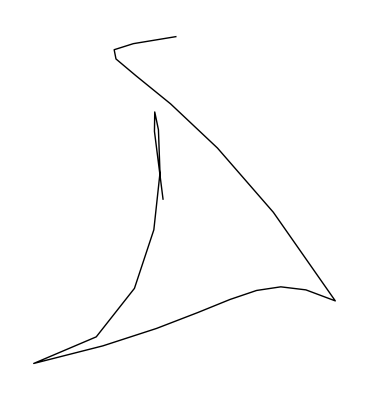

```mathematica
RandomBezierCurve[10,10]
```

Generate a random 3D Bezier curve with 24 points:

```mathematica
RandomBezierCurve[10,24,3]
```

-Graphics3D-

### Scope

Text about additional examples expanding scope (and see other sections for options, applications, etc):

```mathematica
MyFunction[x,y,z]
```

x y z

### Options

### Applications

### Properties and Relations

### Possible Issues

### Neat Examples

```mathematica
Graphics[Table[{Hue[RandomReal[]],BezierCurve[RandomReal[1,{4,2}]]},{30}]]
```

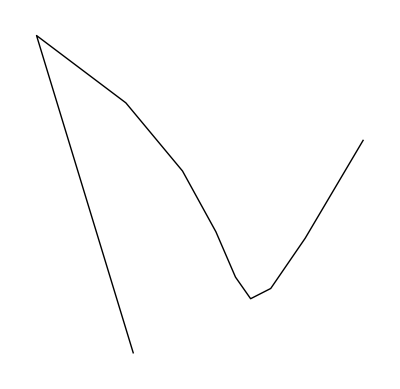

```mathematica
RandomBezierCurve[5,5]
```

```mathematica
AbsoluteOptions[RandomBezierCurve[5,5]]
```

{AlignmentPoint→Center,AspectRatio→1.63485,Axes→False,AxesLabel→None,AxesOrigin→{2.5,1.},AxesStyle→{{},{}},Background→None,BaselinePosition→Automatic,BaseStyle→{},ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction→Identity,Epilog→{},FormatType→TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{{{},{}},{{},{}}},FrameTicks→{{{{0.6,,{0.007266,0.}},{0.8,,{0.007266,0.}},{1.,1,{0.01211,0.}},{1.2,,{0.007266,0.}},{1.4,,{0.007266,0.}},{1.6,,{0.007266,0.}},{1.8,,{0.007266,0.}},{2.,2,{0.01211,0.}},{2.2,,{0.007266,0.}},{2.4,,{0.007266,0.}},{2.6,,{0.007266,0.}},{2.8,,{0.007266,0.}},{3.,3,{0.01211,0.}},{3.2,,{0.007266,0.}},{3.4,,{0.007266,0.}},{3.6,,{0.007266,0.}},{3.8,,{0.007266,0.}},{4.,4,{0.01211,0.}},{4.2,,{0.007266,0.}},{4.4,,{0.007266,0.}},{4.6,,{0.007266,0.}},{4.8,,{0.007266,0.}},{5.,5,{0.01211,0.}}},{{0.6,,{0.007266,0.}},{0.8,,{0.007266,0.}},{1.,,{0.01211,0.}},{1.2,,{0.007266,0.}},{1.4,,{0.007266,0.}},{1.6,,{0.007266,0.}},{1.8,,{0.007266,0.}},{2.,,{0.01211,0.}},{2.2,,{0.007266,0.}},{2.4,,{0.007266,0.}},{2.6,,{0.007266,0.}},{2.8,,{0.007266,0.}},{3.,,{0.01211,0.}},{3.2,,{0.007266,0.}},{3.4,,{0.007266,0.}},{3.6,,{0.007266,0.}},{3.8,,{0.007266,0.}},{4.,,{0.01211,0.}},{4.2,,{0.007266,0.}},{4.4,,{0.007266,0.}},{4.6,,{0.007266,0.}},{4.8,,{0.007266,0.}},{5.,,{0.01211,0.}}}},{{{2.1,,{0.007266,0.}},{2.2,,{0.007266,0.}},{2.3,,{0.007266,0.}},{2.4,,{0.007266,0.}},{2.5,2.5,{0.01211,0.}},{2.6,,{0.007266,0.}},{2.7,,{0.007266,0.}},{2.8,,{0.007266,0.}},{2.9,,{0.007266,0.}},{3.,3.0,{0.01211,0.}},{3.1,,{0.007266,0.}},{3.2,,{0.007266,0.}},{3.3,,{0.007266,0.}},{3.4,,{0.007266,0.}},{3.5,3.5,{0.01211,0.}},{3.6,,{0.007266,0.}},{3.7,,{0.007266,0.}},{3.8,,{0.007266,0.}},{3.9,,{0.007266,0.}},{4.,4.0,{0.01211,0.}},{4.1,,{0.007266,0.}},{4.2,,{0.007266,0.}},{4.3,,{0.007266,0.}},{4.4,,{0.007266,0.}},{4.5,4.5,{0.01211,0.}},{4.6,,{0.007266,0.}},{4.7,,{0.007266,0.}}},{{2.1,,{0.007266,0.}},{2.2,,{0.007266,0.}},{2.3,,{0.007266,0.}},{2.4,,{0.007266,0.}},{2.5,,{0.01211,0.}},{2.6,,{0.007266,0.}},{2.7,,{0.007266,0.}},{2.8,,{0.007266,0.}},{2.9,,{0.007266,0.}},{3.,,{0.01211,0.}},{3.1,,{0.007266,0.}},{3.2,,{0.007266,0.}},{3.3,,{0.007266,0.}},{3.4,,{0.007266,0.}},{3.5,,{0.01211,0.}},{3.6,,{0.007266,0.}},{3.7,,{0.007266,0.}},{3.8,,{0.007266,0.}},{3.9,,{0.007266,0.}},{4.,,{0.01211,0.}},{4.1,,{0.007266,0.}},{4.2,,{0.007266,0.}},{4.3,,{0.007266,0.}},{4.4,,{0.007266,0.}},{4.5,,{0.01211,0.}},{4.6,,{0.007266,0.}},{4.7,,{0.007266,0.}}}}},FrameTicksStyle→{{{},{}},{{},{}}},GridLines→None,GridLinesStyle→{{},{}},ImageMargins→0.,ImagePadding→{{0.,0.},{0.,0.}},ImageSize→{264.244,432.},ImageSizeRaw→Automatic,LabelStyle→{},Method→{},PlotLabel→None,PlotRange→{{2.06589,4.71398},{0.575284,4.97896}},PlotRangeClipping→False,PlotRangePadding→{{0.0551684,0.0551684},{0.0529616,0.0529616}},PlotRegion→{{0.,1.},{0.,1.}},PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,Ticks→{None,None},TicksStyle→{{},{}}}

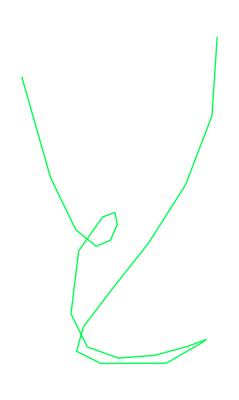

```mathematica
RandomBezierCurve[10,{-6,6},Hue[RandomReal[]]]
```

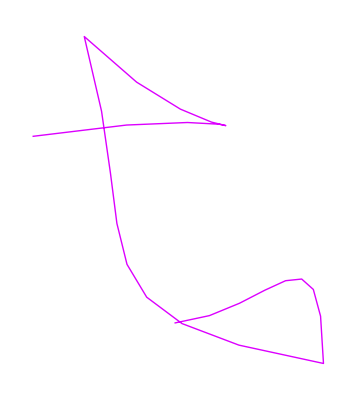

```mathematica
RandomBezierCurve[10,{-6,6},Hue[RandomReal[]],5]
```

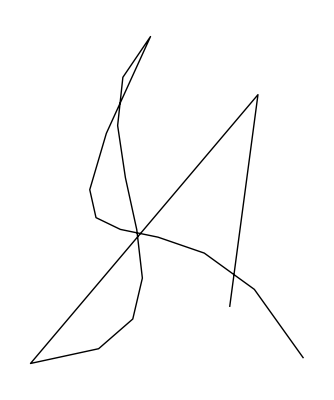

```mathematica
RandomBezierCurve[9,{-6,6},5]
```

```mathematica
Hold[RandomBezierCurve[10,{-6,6},5]]
```

Hold[RandomBezierCurve[10,{-6,6},5]]

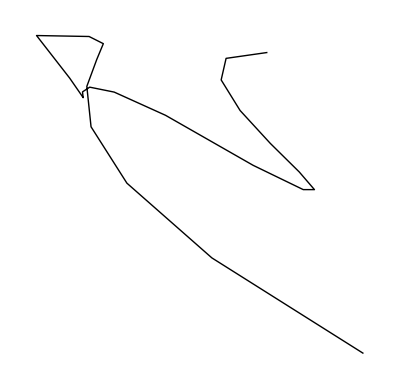
Hold[-Graphics-]

```mathematica
MapAt[Evaluate,Hold[RandomBezierCurve[10,{-6,6},5]],1]
```

```mathematica
Table[BezierCurve[RandomReal[5,{2,5}]]]
```

BezierCurve[{{0.0349917,1.88003,3.08719,0.952662,4.38805},{0.741925,2.44355,0.521018,3.6317,2.60252}}]

```mathematica
Table[{Hue[RandomReal[]],BezierCurve[RandomReal[1,{4,2}]]},{30}]
```

{{Hue[0.37110026968229426],BezierCurve[{{0.775425,0.396309},{0.724046,0.185055},{0.851415,0.523523},{0.387157,0.757324}}]},{Hue[0.6606895655523486],BezierCurve[{{0.704804,0.930246},{0.367283,0.677011},{0.929554,0.0430602},{0.71733,0.78087}}]},{Hue[0.7880074892239337],BezierCurve[{{0.233047,0.471615},{0.0508958,0.308889},{0.912614,0.459629},{0.48033,0.80708}}]},{Hue[0.42310998535425215],BezierCurve[{{0.636902,0.66571},{0.426758,0.963987},{0.750347,0.315513},{0.144041,0.550805}}]},{Hue[0.12451489601898835],BezierCurve[{{0.0311194,0.773576},{0.484234,0.640205},{0.175205,0.772717},{0.692029,0.0326159}}]},{Hue[0.6763324681758953],BezierCurve[{{0.531152,0.54269},{0.778848,0.937857},{0.442015,0.340495},{0.872437,0.903955}}]},{Hue[0.6456925419514286],BezierCurve[{{0.10428,0.82934},{0.103214,0.291697},{0.6376,0.849836},{0.803435,0.0901017}}]},{Hue[0.8164633444278198],BezierCurve[{{0.796681,0.491425},{0.0771248,0.490489},{0.723908,0.462783},{0.71929,0.97838}}]},{Hue[0.7399805545363667],BezierCurve[{{0.0959247,0.145508},{0.611101,0.359354},{0.994285,0.214777},{0.0641336,0.329496}}]},{Hue[0.8132037311005893],BezierCurve[{{0.995841,0.0509544},{0.474818,0.131921},{0.132817,0.970564},{0.77124,0.454071}}]},{Hue[0.6220305733210607],BezierCurve[{{0.829268,0.0749061},{0.580225,0.0200347},{0.230749,0.422183},{0.604383,0.0788977}}]},{Hue[0.9094492522153617],BezierCurve[{{0.0617865,0.565511},{0.464694,0.360964},{0.140088,0.702693},{0.853253,0.708702}}]},{Hue[0.18697613066902785],BezierCurve[{{0.363829,0.391008},{0.363498,0.0127893},{0.569441,0.334801},{0.652603,0.73724}}]},{Hue[0.9112915270028923],BezierCurve[{{0.497327,0.687812},{0.600383,0.496569},{0.0159077,0.796405},{0.362442,0.371461}}]},{Hue[0.4258512096218199],BezierCurve[{{0.348147,0.165047},{0.749314,0.24524},{0.275567,0.978801},{0.57264,0.530638}}]},{Hue[0.4802111565727214],BezierCurve[{{0.242033,0.417671},{0.881928,0.504651},{0.37157,0.141825},{0.173695,0.273486}}]},{Hue[0.9523454967564593],BezierCurve[{{0.820665,0.373885},{0.338681,0.163665},{0.212957,0.680417},{0.452883,0.177418}}]},{Hue[0.3212790106004637],BezierCurve[{{0.9442,0.375102},{0.137248,0.975148},{0.868533,0.598296},{0.536175,0.681528}}]},{Hue[0.36344902344684127],BezierCurve[{{0.574309,0.132334},{0.567572,0.0363687},{0.992201,0.307974},{0.999854,0.0705722}}]},{Hue[0.3944378949580549],BezierCurve[{{0.713436,0.615792},{0.421421,0.896528},{0.581088,0.217454},{0.325959,0.988037}}]},{Hue[0.5173061469128561],BezierCurve[{{0.527424,0.00933475},{0.557026,0.0444897},{0.994471,0.672324},{0.74954,0.707058}}]},{Hue[0.266541700357408],BezierCurve[{{0.402379,0.504939},{0.574854,0.0408286},{0.377228,0.282291},{0.440085,0.402013}}]},{Hue[0.9511109098926922],BezierCurve[{{0.492209,0.466815},{0.127266,0.384431},{0.906577,0.302556},{0.0832067,0.605667}}]},{Hue[0.11735460951263654],BezierCurve[{{0.555414,0.0682909},{0.0716062,0.98486},{0.749266,0.240345},{0.735584,0.3901}}]},{Hue[0.43789135160361914],BezierCurve[{{0.343309,0.846255},{0.781525,0.918691},{0.240369,0.0450549},{0.591539,0.187445}}]},{Hue[0.7759730871886219],BezierCurve[{{0.0891913,0.628137},{0.246525,0.182652},{0.433441,0.654319},{0.807598,0.302441}}]},{Hue[0.8708502394893511],BezierCurve[{{0.530036,0.288618},{0.66692,0.138999},{0.200577,0.0910803},{0.43711,0.268114}}]},{Hue[0.13402689635729748],BezierCurve[{{0.972101,0.172743},{0.212894,0.593536},{0.447332,0.917137},{0.185248,0.726174}}]},{Hue[0.6559421811787187],BezierCurve[{{0.610851,0.912313},{0.921114,0.490355},{0.49597,0.063215},{0.162358,0.145337}}]},{Hue[0.6367249371083801],BezierCurve[{{0.201243,0.118786},{0.482711,0.432055},{0.588863,0.550219},{0.841337,0.0352709}}]}}

```mathematica
RandomBezierCurve[count_?IntegerQ,{lower_,upper_},n_?IntegerQ,options:OptionsPattern[Graphics]]:=Graphics[Table[BezierCurve[RandomReal[{lower,upper},{count,2}]],{n}],options]/;(count>0∧n>0)
```

```mathematica
Table[BezierCurve[RandomReal[{-10,10},{5,2}]],{11}]
```

{BezierCurve[{{-5.17112,-5.95647},{-3.11463,7.07488},{-6.41713,6.53473},{0.255043,3.94488},{-9.45117,-8.314}}],BezierCurve[{{-7.18968,-8.76331},{-3.577,1.58626},{-4.49855,9.81011},{6.94083,2.23668},{6.11312,1.3924}}],BezierCurve[{{-6.35772,0.181776},{-0.336529,-7.92313},{-8.61669,9.96632},{-7.36757,3.42671},{-5.3497,-9.1586}}],BezierCurve[{{-1.5547,-3.77929},{7.9979,1.65288},{-3.1605,3.99201},{-1.85206,-8.7536},{-4.5494,8.51178}}],BezierCurve[{{3.94689,-4.57489},{5.38409,9.41096},{0.378291,-0.267703},{5.57104,9.05663},{-1.42275,-7.03206}}],BezierCurve[{{3.81349,-4.454},{-5.51699,-2.4506},{2.59849,8.8382},{-8.33301,9.51404},{-0.838922,-1.73145}}],BezierCurve[{{-2.79112,2.22863},{6.12046,5.05968},{-7.90177,3.58363},{-0.381028,0.447668},{-2.45542,7.64415}}],BezierCurve[{{4.85307,-1.65154},{-4.92637,-4.76473},{8.2585,-4.48598},{8.20104,2.2702},{7.16837,1.59434}}],BezierCurve[{{-5.33027,9.22738},{2.20144,-6.90467},{-2.38905,6.80566},{-1.07614,6.52602},{5.82813,-7.92559}}],BezierCurve[{{-6.76798,-6.54138},{-6.71729,-2.74631},{-6.4758,-4.00213},{8.62307,8.9708},{5.78613,-8.46953}}],BezierCurve[{{5.55527,-8.2954},{6.74074,9.93023},{-0.388801,-5.09492},{5.32422,-7.79037},{4.49123,8.55274}}]}

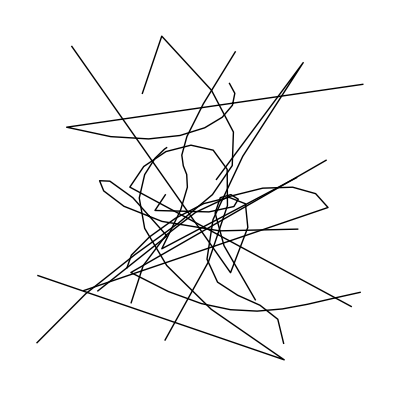

```mathematica
Graphics[Table[BezierCurve[RandomReal[{-10,10},{5,2}]],{11}]]
```

```mathematica
RandomBezierCurve[count_?IntegerQ,{lower_,upper_},n_?IntegerQ,options:OptionsPattern[Graphics]]:=Graphics[Table[BezierCurve[RandomReal[{lower,upper},{count,2}]],{n}],options]/;(count>0∧n>0)
```

```mathematica
RandomBezierCurve[count_?IntegerQ,{lower_,upper_},2,n_?IntegerQ,options:OptionsPattern[Graphics]]:=Graphics[Table[BezierCurve[RandomReal[{-10,10},{5,2}]],{11}]]
```

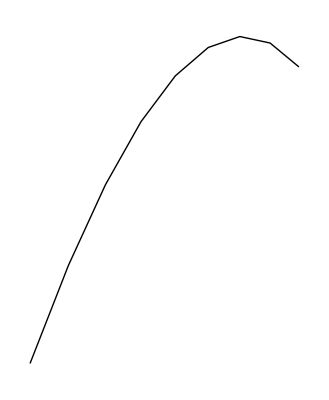

```mathematica
RandomBezierCurve[3,{-10,10},2,7]
```

### Example Program

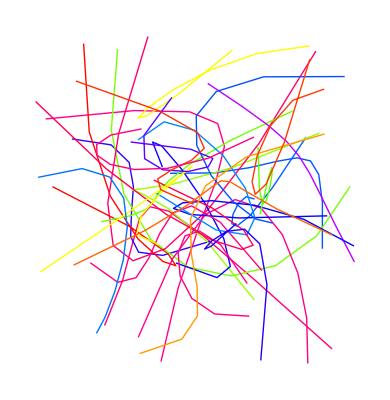

```mathematica
Graphics[Table[{Hue[RandomReal[]],BezierCurve[RandomReal[1,{4,2}]]},{30}]]
```

```mathematica
ClearAll[RandomBezierCurve]
RandomBezierCurve[pointcount_]:=Graphics[{BezierCurve[RandomReal[1,{pointcount,2}]]}]
RandomBezierCurve[pointcount_,n_]:=Graphics[Table[{BezierCurve[RandomReal[1,{pointcount,2}]]},{n}]]
```

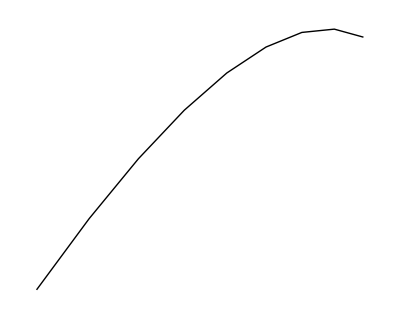

```mathematica
RandomBezierCurve[3]
```

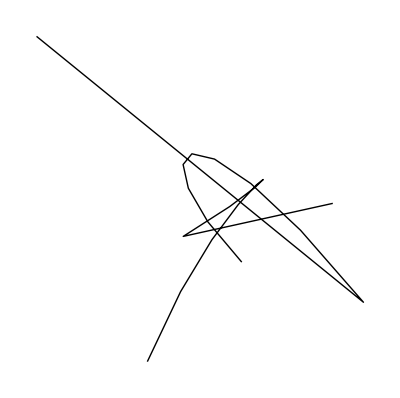

```mathematica
RandomBezierCurve[5,2]
```

## Source & Additional Information

### Contributed By

Author Name

### Keywords

keyword 1

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

SymbolName (documented Wolfram Language symbol)

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.